# Minimal regulation network for slope antagonism

## Three node networks

In this section we try to find the minimal regulation network that can explain slope antagonism. For this we first look at all possible three node networks excluding the symmetric cases. We find the following 9 networks-

```mathematica
{}
```

```mathematica
{-Graphics-}
```

We analyze each of these nine networks using- -Graphics-

## Network A

Equation for the dynamics of M-

```mathematica
dmdt=Subscript[k, m0]+Subscript[k, m1]*Subscript[s, 1]+Subscript[k, m2]*Subscript[s, 2]-Subscript[k, dm]*m;
```

We can solve for m as-

```mathematica
Solve[dmdt==0,m]
```

{{m→(k_m0+k_m1 s_1+k_m2 s_2)/k_dm}}

#### Surface map and derivatives of M

We want to check if network A can explain slope antagonism topologically. For that we set all reaction rates to 1, Δs_1 and Δs_2 to 1 and look at the surface maps and derivatives. So for analysis and plots m is-

```mathematica
mP=(1+1* Subscript[s, 1]+1* Subscript[s, 2])/1;
```

When only individual signals are present,

```mathematica
mP1=Subscript[s, 1];
mP2=Subscript[s, 2];
```

So, we now look at the derivatives,

```mathematica
Subscript[m, 1]=D[mP1,Subscript[s, 1]]
```

1

```mathematica
Subscript[m, 2]=D[mP2,Subscript[s, 2]]
```

1

```mathematica
Subscript[m, 12]=D[mP,Subscript[s, 1]]+D[mP,Subscript[s, 2]]
```

2

#### So, m_12>{m_1,m_2}, hence network A cannot show slope antagonism. The surface plots looks like-

```mathematica
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large]
```

-Graphics3D-

## Network B

Equation for the dynamics of M -

```mathematica
dmdt=Subscript[k, m0]+Subscript[k, m2]*Subscript[s, 2]-Subscript[k, dm]*m-Subscript[k, m1]*Subscript[s, 1]*m;
```

We can solve for m as -

```mathematica
Solve[dmdt==0,m]
```

{{m→(k_m0+k_m2 s_2)/(k_dm+k_m1 s_1)}}

#### Surface map and derivatives of M

```mathematica
mP=(1+1* Subscript[s, 2])/(1+1* Subscript[s, 1]);
```

```mathematica
mP1=1/(1+Subscript[s, 1]);
mP2=1+Subscript[s, 2];
```

The derivatives are,

```mathematica
Subscript[m, 1]=D[mP1,Subscript[s, 1]]
```

-1/(1+s_1)^2

```mathematica
Subscript[m, 2]=D[mP2,Subscript[s, 2]]
```

1

```mathematica
Subscript[m, 12]=FullSimplify[D[mP,Subscript[s, 1]]+D[mP,Subscript[s, 2]]]
```

(s_1-s_2)/(1+s_1)^2

#### So, m_1<0, hence network B cannot satisfy the slope antagonism condition.

```mathematica
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

## Network C

Equation for the dynamics of M -

```mathematica
dmdt=Subscript[k, m0]-Subscript[k, dm]*m-Subscript[k, m1]*Subscript[s, 1]*m-Subscript[k, m2]*Subscript[s, 2]*m;
```

The solution for m is-

```mathematica
Solve[dmdt==0,m]
```

{{m→k_m0/(k_dm+k_m1 s_1+k_m2 s_2)}}

#### Surface map and derivatives of M

```mathematica
mP=1/(1+Subscript[s, 1]+Subscript[s, 2]);
```

```mathematica
mP1=1/(1+Subscript[s, 1]);
mP2=1/(1+Subscript[s, 2]);
```

The derivatives are,

```mathematica
Subscript[m, 1]=D[mP1,Subscript[s, 1]]
```

-1/(1+s_1)^2

```mathematica
Subscript[m, 2]=D[mP2,Subscript[s, 2]]
```

-1/(1+s_2)^2

```mathematica
Subscript[m, 12]=FullSimplify[D[mP,Subscript[s, 1]]+D[mP,Subscript[s, 2]]]
```

-2/(1+s_1+s_2)^2

#### So, m_1<0,m_2<0 hence network C cannot satisfy the slope antagonism condition.

```mathematica
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

## Network D

Equation for the dynamics of M -

```mathematica
dmdt=Subscript[k, m0]+Subscript[k, m1]*Subscript[s, 1]+Subscript[k, m2]*Subscript[s, 2]-(Subscript[k, dm]+Subscript[k, mm]*m)*m;
```

The solution for m is -

```mathematica
Solve[dmdt==0,m]
```

{{m→-(k_dm-√(k_dm^2+4 k_mm (k_m0+k_m1 s_1+k_m2 s_2)))/(2 k_mm)},{m→-(k_dm+√(k_dm^2+4 k_mm (k_m0+k_m1 s_1+k_m2 s_2)))/(2 k_mm)}}

#### Surface map and derivatives of M

```mathematica
mP=(-1+√(1+4*(1+Subscript[s, 1]+Subscript[s, 2])))/2;
mP1=(-1+√(1+4*(1+Subscript[s, 1])))/2;
mP2=(-1+√(1+4*(1+Subscript[s, 2])))/2;
```

The derivatives are,

```mathematica
Subscript[m, 1]=D[mP1,Subscript[s, 1]]
```

1/(√(1+4 (1+s_1)))

```mathematica
Subscript[m, 2]=D[mP2,Subscript[s, 2]]
```

1/(√(1+4 (1+s_2)))

```mathematica
Subscript[m, 12]=FullSimplify[D[mP,Subscript[s, 1]]+D[mP,Subscript[s, 2]]]
```

2/(√(5+4 s_1+4 s_2))

```mathematica
FullSimplify[Subscript[m, 12]^2-Subscript[m, 1]^2]
```

1/(-5-4 s_1)+4/(5+4 s_1+4 s_2)

```mathematica
FullSimplify[Subscript[m, 12]^2-Subscript[m, 2]^2]
```

1/(-5-4 s_2)+4/(5+4 s_1+4 s_2)

```mathematica
Solve[Subscript[m, 12]^2==Subscript[m, 1]^2,Subscript[s, 2]]
```

{{s_2→3/4 (5+4 s_1)}}

So, if we want m_12<m_1 then we need s_2>3/4 (5+4 s_1)

```mathematica
Solve[Subscript[m, 12]^2==Subscript[m, 2]^2,Subscript[s, 2]]
```

{{s_2→1/12 (-15+4 s_1)}}

So, if we want m_12<m_2 then we need s_2<1/12 (-15+4 s_1)

#### Now, to satisfy m_12<{m_1,m_2} we need 3/4 (5+4 s_1)< s_2<1/12 (-15+4 s_1). Which can only be satisfied if 3/4 (5+4 s_1)<1/12 (-15+4 s_1)→ s_1<-15/8. But we know s_1 must be positive. So, the slope antagonism condition cannot be satisfied.

```mathematica
Subscript[s, c21]=3/4 (5+4 Subscript[s, 1]);
Subscript[s, c22]=1/12 (-15+4 Subscript[s, 1]);
```

```mathematica
Plot3D[1/(-5-4 Subscript[s, 1])+4/(5+4 Subscript[s, 1]+4 Subscript[s, 2]),{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

1/(-5-4 s_1)+4/(5+4 s_1+4 s_2)

So, m_1=1/(5+4 s_1)^0.5 =2/(20+16 s_1)^0.5 , m_2=2/(20+16 s_2)^0.5

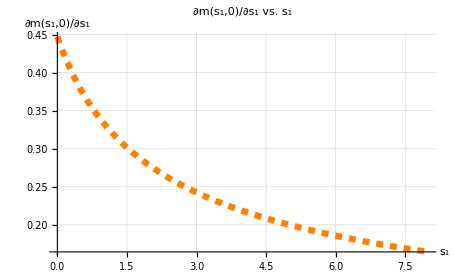

```mathematica
plotset={PlotStyle->Thick,AxesStyle->Thick,FrameStyle->Thick, TicksStyle->Directive[Black,15]};
plotline1=Plot[Subscript[m, 1],{Subscript[s, 1],0,8}, 
AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["∂m(s_1,0)/∂s_1",Bold,15,FontColor->Black]},
PlotLabel->Style["∂m(s_1,0)/∂s_1 vs. s_1",Bold,20,FontColor->Black],
GridLines->Automatic,
PlotStyle->{Orange,Dashed,Thickness[0.01]},Evaluate@plotset]
```

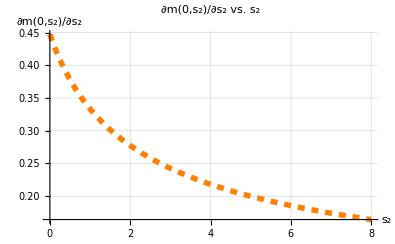

```mathematica
plotline2=Plot[Subscript[m, 2],{Subscript[s, 2],0,8}, 
AxesLabel->{Style["s_2",Bold,20,FontColor->Black],Style["∂m(0,s_2)/∂s_2",Bold,15,FontColor->Black]},
PlotLabel->Style["∂m(0,s_2)/∂s_2 vs. s_2",Bold,20,FontColor->Black],
GridLines->Automatic,
PlotStyle->{Orange,Dashed,Thickness[0.01]},Evaluate@plotset]
```

```mathematica
plotsurface=Plot3D[Subscript[m, 12],{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["∇m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["∇m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

## Network E

Dynamical equation for M-

```mathematica
dmdt=Subscript[k, m0]+Subscript[k, m2]*Subscript[s, 2]-(Subscript[k, dm]+Subscript[k, m1]*Subscript[s, 1]+Subscript[k, mm]*m)*m;
Solve[dmdt==0,m]
```

{{m→-(k_dm+k_m1 s_1-√((-k_dm-k_m1 s_1)^2+4 k_mm (k_m0+k_m2 s_2)))/(2 k_mm)},{m→-(k_dm+k_m1 s_1+√((-k_dm-k_m1 s_1)^2+4 k_mm (k_m0+k_m2 s_2)))/(2 k_mm)}}

Using m>0 and setting all reaction rates to 1 for analysis we have-

```mathematica
mP=(-1-Subscript[s, 1]+√((-1-Subscript[s, 1])^2+4 *(1+Subscript[s, 2])))/2;
mP1=(-1-Subscript[s, 1]+√((-1-Subscript[s, 1])^2+4))/2;
mP2=(-1+√(1+4 *(1+Subscript[s, 2])))/2;
```

Now we derive the derivatives

```mathematica
Subscript[m, 1]=FullSimplify[D[mP1,Subscript[s, 1]]]
```

1/2 (-1+(1+s_1)/(√(5+s_1 (2+s_1))))

```mathematica
FullSimplify[5+Subscript[s, 1] (2+Subscript[s, 1])-(1+Subscript[s, 1])^2]
```

4

#### So, we can see that m_1<0. So, that is why network E fails.

```mathematica
Subscript[m, 2]=FullSimplify[D[mP2,Subscript[s, 2]]]
```

1/(√(5+4 s_2))

```mathematica
Subscript[m, 12]=FullSimplify[D[mP,Subscript[s, 1]]+D[mP,Subscript[s, 2]]]
```

(3+s_1-√(5+s_1 (2+s_1)+4 s_2))/(2 √(5+s_1 (2+s_1)+4 s_2))

The surface plot-

```mathematica
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

## Network F

The dynamics of M is-

```mathematica
dmdt=Subscript[k, m0]-(Subscript[k, dm]+Subscript[k, m1]*Subscript[s, 1]+Subscript[k, m2]*Subscript[s, 2]+Subscript[k, mm]*m)*m;
Solve[dmdt==0,m]
```

{{m→-(k_dm+k_m1 s_1+k_m2 s_2-√(4 k_m0 k_mm+(-k_dm-k_m1 s_1-k_m2 s_2)^2))/(2 k_mm)},{m→-(k_dm+k_m1 s_1+k_m2 s_2+√(4 k_m0 k_mm+(-k_dm-k_m1 s_1-k_m2 s_2)^2))/(2 k_mm)}}

To plot and analyse we set all reaction rates to 1 and use the condition that m>0-

```mathematica
mP=(-1-Subscript[s, 1]-Subscript[s, 2]+√(4 +(-1-Subscript[s, 1]-Subscript[s, 2])^2))/2;
mP1=(-1-Subscript[s, 1]+√(4 +(-1-Subscript[s, 1])^2))/2;
mP2=(-1-Subscript[s, 2]+√(4 +(-1-Subscript[s, 2])^2))/2;
```

Derivative analysis for slope antagonism-

```mathematica
Subscript[m, 1]=FullSimplify[D[mP1,Subscript[s, 1]]]
```

1/2 (-1+(1+s_1)/(√(5+s_1 (2+s_1))))

```mathematica
Subscript[m, 2]=FullSimplify[D[mP2,Subscript[s, 2]]]
```

1/2 (-1+(1+s_2)/(√(5+s_2 (2+s_2))))

```mathematica
Subscript[m, 12]=FullSimplify[D[mP,Subscript[s, 1]]+D[mP,Subscript[s, 2]]]
```

-1+(1+s_1+s_2)/(√(4+(1+s_1+s_2)^2))

#### Using network E’s analysis we see {m_1,m_2}<0. So network F also fails.

Surface plot for m-

```mathematica
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

## Network G

The dynamics of M-

```mathematica
dmdt=Subscript[k, m0]+Subscript[k, m1]*Subscript[s, 1]+Subscript[k, m2]*Subscript[s, 2]-(Subscript[k, dm]-Subscript[k, pm])*m;
Solve[dmdt==0,m]
```

{{m→(k_m0+k_m1 s_1+k_m2 s_2)/(k_dm-k_pm)}}

Now for positivity of m and to have a steady state solution we need k_dm>k_pm. So, in this case, for further analysis we set all rates except k_dm to 1 and set k_dm=2.

```mathematica
mP=1+Subscript[s, 1]+Subscript[s, 2];
mP1=1+Subscript[s, 1];
mP2=1+Subscript[s, 2];
```

The derivatives of m-

```mathematica
Subscript[m, 1]=FullSimplify[D[mP1,Subscript[s, 1]]]
```

1

```mathematica
Subscript[m, 2]=FullSimplify[D[mP2,Subscript[s, 2]]]
```

1

```mathematica
Subscript[m, 12]=FullSimplify[D[mP,Subscript[s, 1]]+D[mP,Subscript[s, 2]]]
```

2

#### So, in this case m_12>{m_1,m_2}, that is why network G fails.

Surface plot of m-

```mathematica
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

### Now network H and I will have the exact same characteristics as network B and C respectively, and they will be unsuccessful for the same reasons. We now analyse four node three edge networks.

## Four node three edges regulatory networks

We consider these six unique four node three edges regulatory networks-

```mathematica
{-Graphics-}
```

#### Now, in networks A,B,C m is produced by A using a simple production reaction. So, in these networks M will behave in exactly the same way as in the corresponding three node networks A,B,C respectively. Hence, networks A,B,C are unsuccessful to explain the slope antagonism for exactly the same reasons as in the three node case. Now, we analyze networks D-F.

## Network D

Dynamics of A and M-

```mathematica
dadt=Subscript[k, a0]+Subscript[k, a1]*Subscript[s, 1]+Subscript[k, a2]*Subscript[s, 2]-Subscript[k, da]*a;
dmdt=Subscript[k, m0]-(Subscript[k, dm]+Subscript[k, am]*a)*m;
Solve[{dadt==0,dmdt==0},{a,m}]
```

{{a→(k_a0+k_a1 s_1+k_a2 s_2)/k_da,m→(k_da k_m0)/(k_a0 k_am+k_da k_dm+k_a1 k_am s_1+k_a2 k_am s_2)}}

We take the value of each parameter to be 1 then m is-

```mathematica
mP=1/(2+Subscript[s, 1]+Subscript[s, 2]);
mP1=1/(2+Subscript[s, 1]);
mP2=1/(2+Subscript[s, 2]);
```

We now calculate the derivatives-

```mathematica
Subscript[m, 1]=FullSimplify[D[mP1,Subscript[s, 1]]]
```

-1/(2+s_1)^2

```mathematica
Subscript[m, 2]=FullSimplify[D[mP2,Subscript[s, 2]]]
```

-1/(2+s_2)^2

```mathematica
Subscript[m, 12]=FullSimplify[D[mP,Subscript[s, 1]]+D[mP,Subscript[s, 2]]]
```

-2/(2+s_1+s_2)^2

#### Here, we have {m_1,m_2}<0. So, network D fails.

Surface plot of m-

```mathematica
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

## Network E

The dynamics of A,M-

```mathematica
dadt=Subscript[k, a0]+Subscript[k, a2]*Subscript[s, 2]-(Subscript[k, da]+Subscript[k, a1]*Subscript[s, 1])*a;
dmdt=Subscript[k, m0]-(Subscript[k, dm]+Subscript[k, am]*a)*m;
Solve[{dadt==0,dmdt==0},{a,m}]
```

{{a→(k_a0+k_a2 s_2)/(k_da+k_a1 s_1),m→(k_m0 (k_da+k_a1 s_1))/(k_a0 k_am+k_da k_dm+k_a1 k_dm s_1+k_a2 k_am s_2)}}

For plotting we take each parameter value to be 1. Then we have,

```mathematica
mP=(1+Subscript[s, 1])/(2+Subscript[s, 1]+Subscript[s, 2]);
mP1=(1+Subscript[s, 1])/(2+Subscript[s, 1]);
mP2=1/(2+Subscript[s, 2]);
```

Calculating the derivatives,

```mathematica
Subscript[m, 1]=FullSimplify[D[mP1,Subscript[s, 1]]]
```

1/(2+s_1)^2

```mathematica
Subscript[m, 2]=FullSimplify[D[mP2,Subscript[s, 2]]]
```

-1/(2+s_2)^2

```mathematica
Subscript[m, 12]=FullSimplify[D[mP,Subscript[s, 1]]+D[mP,Subscript[s, 2]]]
```

(-s_1+s_2)/(2+s_1+s_2)^2

#### Here, we have m_2<0. So, network E fails.

Surface plot of m-

```mathematica
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-

## Network F

The dynamics of A,M is-

```mathematica
dadt=Subscript[k, a0]-(Subscript[k, da]+Subscript[k, a1]*Subscript[s, 1]+Subscript[k, a2]*Subscript[s, 2])*a;
dmdt=Subscript[k, m0]-(Subscript[k, dm]+Subscript[k, am]*a)*m;
Solve[{dadt==0,dmdt==0},{a,m}]
```

{{a→k_a0/(k_da+k_a1 s_1+k_a2 s_2),m→(k_m0 (k_da+k_a1 s_1+k_a2 s_2))/(k_a0 k_am+k_da k_dm+k_a1 k_dm s_1+k_a2 k_dm s_2)}}

For plotting we set all parameter values to 1,

```mathematica
mP=(1+Subscript[s, 1]+Subscript[s, 2])/(2+Subscript[s, 1]+Subscript[s, 2]);
mP1=(1+Subscript[s, 1])/(2+Subscript[s, 1]);
mP2=(1+Subscript[s, 2])/(2+Subscript[s, 2]);
```

The derivatives are,

```mathematica
Subscript[m, 1]=FullSimplify[D[mP1,Subscript[s, 1]]]
```

1/(2+s_1)^2

```mathematica
Subscript[m, 2]=FullSimplify[D[mP2,Subscript[s, 2]]]
```

1/(2+s_2)^2

```mathematica
Subscript[m, 12]=FullSimplify[D[mP,Subscript[s, 1]]+D[mP,Subscript[s, 2]]]
```

2/(2+s_1+s_2)^2

```mathematica
FullSimplify[Subscript[m, 12]-Subscript[m, 2]]
```

-1/(2+s_2)^2+2/(2+s_1+s_2)^2

```mathematica
Solve[Subscript[m, 12]==Subscript[m, 1],Subscript[s, 2]]
```

{{s_2→-2-s_1-√2 √(4+4 s_1+s_1^2)},{s_2→-2-s_1+√2 √(4+4 s_1+s_1^2)}}

```mathematica
Subscript[s, c21]=(2+Subscript[s, 1])*(√2-1);
Subscript[s, c22]=Subscript[s, 1]*(√2+1)-2;
FullSimplify[Subscript[s, c22]-Subscript[s, c21]]
```

-2 √2+2 s_1

#### We want s_c21<s_2<s_c22.

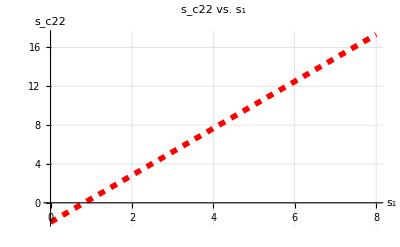

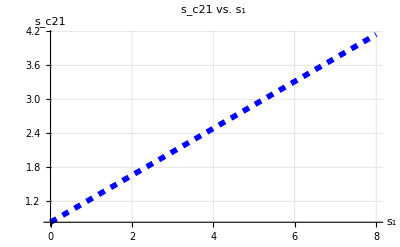

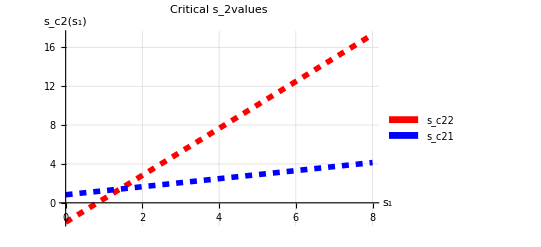

```mathematica
plotset={PlotStyle->Thick,AxesStyle->Thick,FrameStyle->Thick, TicksStyle->Directive[Black,15]};
plot1=Plot[Subscript[s, c22],{Subscript[s, 1],0,8}, 
AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_c22",Bold,20,FontColor->Black]},
PlotLabel->Style["s_c22 vs. s_1",Bold,30,FontColor->Black],
GridLines->Automatic,
PlotStyle->{Red,Dashed,Thickness[0.01]},Evaluate@plotset]
plot2=Plot[Subscript[s, c21],{Subscript[s, 1],0,8}, 
AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_c21",Bold,20,FontColor->Black]},
PlotLabel->Style["s_c21 vs. s_1",Bold,30,FontColor->Black],
GridLines->Automatic,
PlotStyle->{Blue,Dashed,Thickness[0.01]},Evaluate@plotset]
Legended[Show[plot1,plot2,PlotLabel-> "Critical s_2values",
AxesLabel-> {"s_1","s_c2(s_1)"},
PlotRange-> All,
GridLines-> Automatic],
SwatchLegend[{Red, Blue},{"s_c22","s_c21"}]]
```

### So we can have {m_1,m_2}>0 and m_12<{m_1,m_2}, for a set of values of (s_1,s_2). Hence slope antagonism can be satisfied by Network F.

Surface plot of m-

```mathematica
Plot3D[mP,{Subscript[s, 1],0,8},{Subscript[s, 2],0,8},AxesLabel->{Style["s_1",Bold,20,FontColor->Black],Style["s_2",Bold,20,FontColor->Black],Style["m(s_(1,)s_2)",Bold,20,FontColor->Black]},
PlotLabel->Style["m(s_(1,)s_2)",Bold,30,FontColor->Black],
ColorFunction->"Rainbow",AxesStyle->Thickness[0.005],BoxStyle->GrayLevel[2], TicksStyle->Directive[Black,15],ImageSize->Large,PlotRange->Full]
```

-Graphics3D-